# Ejercicio : PushDown Automata

Estudiante : Andrey Arguedas Espinoza - 2020426569

## Código

Definimos la función POP

```mathematica
SetAttributes[Pop,HoldAll]
Pop[string_]:=Check[{StringTake[string,1],Check[string=StringDrop[string,1],string=""]},{"",""}]
```

Definimos la función PUSH

```mathematica
Push[string_,a_]:=StringInsert[string,a,1]
```

Hay que notar que el push retorna un string con el push aplicado, pero no modifica el original

```mathematica
ShowGraphFA[edges_,states_List,q0_,q_List,edgelabels_]:=Graph[
edges,
VertexSize->0.25,
VertexLabels->Placed["Name",Center],
VertexStyle->Join[{0->White},Map[(#->Red)&,q]],
EdgeWeight->edgelabels,
EdgeLabels->"EdgeWeight"
]
```

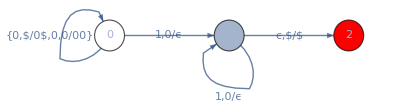

```mathematica
ShowGraphFA[{0->0,0->1,1 ->1,1->2},{0,1,2},{0},{2},{"{0,$/0$,0,0/00}","1,0/ϵ","1,0/ϵ","ϵ,$/$"}]
```

```mathematica
DeltaHat[{state_,string_,stack_}]:=Block[{trans, tempstack=stack,tempstring=string},
trans=δ[{state,First[Pop[tempstring]],First[Pop[tempstack]]}];
{First[trans],tempstring,Push[tempstack,Last[trans]]}
]
```

Definimos la asociacion

```mathematica
δ= Association[
{0,"0","$"}->{0,"0$"},
{0,"0","0"}->{0,"00"},
{0,"1","0"}->{1,""},
{1,"1","0"}->{1,""},
{1,"","$"}->{2,"$"}
];
```

```mathematica
NestList[DeltaHat,{0,"01","$"},3]
```

StringTake::take: Cannot take positions 1 through 1 in "".

StringDrop::drop: Cannot drop positions 1 through 1 in "".

{{0,01,$},{0,1,0$},{1,,$},{2,,$}}

```mathematica
NestWhileList[DeltaHat,{0,"01","$"},#⟦2⟧!=""&]
```

{{0,01,$},{0,1,0$},{1,,$}}

Tengo que lograr que den lo mismo

Veamos el ejemplo del palindrome

```mathematica
δ= Association[
{0,"0","$"}->{0,"0$"},
{0,"1","$"}->{0,"1$"},
{0,"0","0"}->{0,"00"},
{0,"0","1"}->{0,"01"},
{0,"1","0"}->{0,"10"},
{0,"1","1"}->{0,"11"},
{0,"","$"}->{1,"$"},
{0,"","0"}->{1,"0"},
{0,"","1"}->{1,"1"},
{1,"0","0"}->{1,""},
{1,"1","1"}->{1,""},
{1,"","$"}->{2,"$"},
{2,"","$"}->{2,"$"}
];
```

```mathematica
NestList[DeltaHat,{0,"1111","$"},5]
```

StringTake::take: Cannot take positions 1 through 1 in "".

StringDrop::drop: Cannot drop positions 1 through 1 in "".

{{0,1111,$},{0,111,1$},{0,11,11$},{0,1,111$},{0,,1111$},{1,,1111$}}

Veamos como podemos generar el arbol completo de expresiones, por ejemplo con 1111, el primer nivel debe generarnos (q0,111,1$) -> esta ya es generada, (q1,1111,$) -> luego a este ultimos se le vuelve aplicar el DELTAHAT.

```mathematica
δ[{1,"","$"}]
```

{2,$}

```mathematica
DeltaHat[{1,"","$"}]
```

StringTake::take: Cannot take positions 1 through 1 in "".

StringDrop::drop: Cannot drop positions 1 through 1 in "".

{2,,$}

Debemos crear una funcion que nos de bajo la configuracion que tenemos a cuales estados podemos llegar por medio de las transiciones EPSILON

```mathematica
Closure[currentState_, currentString_, currentStack_] := First[δ[{currentState,"",currentStack}]];
```

```mathematica
Closure[1, "1111","$"]
```

2

```mathematica
Closure[0, "1111","$"]
```

1

Notemos como en estos casos la transicion epsilon, funcionó, pero veamos el siguiente caso donde el contenido de la pila no nos dejaría

```mathematica
Closure[1, "1111","0$"]
```

KeyAbsent

Con esto vemos que la transicion epsilon si se saca de esa manera

```mathematica
DeltaHatWithEpsilonClosure[{state_,string_,stack_}] := Block[{epsilonNextState,tempstack=stack,tempstring=string},
epsilonNextState=Closure[state,tempstring,tempstack] ;
(*Check[epsilonNextState,]*)
{DeltaHat[{state,string,stack}], Check[DeltaHat[{epsilonNextState, tempstring, tempstack}],{epsilonNextState,tempstring,tempstack}]}

];
```

```mathematica
DeltaHatWithEpsilonClosure[{0,"1111","$"}]
```

StringInsert::string: String expected at position 2 in StringInsert[,{1,1,$},1].

{{0,111,1$},{1,1111,$}}

```mathematica
NestList[DeltaHatWithEpsilonClosure,{0,"1111","$"},5]
```

StringInsert::string: String expected at position 2 in StringInsert[,{1,1,$},1].

{{0,1111,$},{{0,111,1$},{1,1111,$}},DeltaHatWithEpsilonClosure[{{0,111,1$},{1,1111,$}}],DeltaHatWithEpsilonClosure[DeltaHatWithEpsilonClosure[{{0,111,1$},{1,1111,$}}]],DeltaHatWithEpsilonClosure[DeltaHatWithEpsilonClosure[DeltaHatWithEpsilonClosure[{{0,111,1$},{1,1111,$}}]]],DeltaHatWithEpsilonClosure[DeltaHatWithEpsilonClosure[DeltaHatWithEpsilonClosure[DeltaHatWithEpsilonClosure[{{0,111,1$},{1,1111,$}}]]]]}

```mathematica
Closure[1, "1111", "0$"]
```

KeyAbsent